#### fertility

```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory["D:\\MyLearning\\proj\\Skeleton_Analysis_of_Melt_Network"];
```

```mathematica
{thepoints,thelines,theradius}=readSkel["data\\testdata\\mafertility_thinned0.04_skel.ply"];
```

```mathematica
{theJ,theG}=initJG[thepoints,thelines,theradius];
```

Initial graph built!

Basic junctions computed!

2500

2000

1500

1000

500

0

simplified graph done!

```mathematica
theJ⟦;;,1⟧+14
```

{21,25,27,41,42,45,58,67,75,78,82,86,87,88,94,98,99,103,104,115,116,122,127,142,146,151,157,163,180,181,193,203,206,207,209,223,226,232,247,258,260,271,275,277,278,280,284,285,289,293,296,298,302,304,313,315,318,319,335,337,341,342,345,346,350,351,352,354,363,369,394,399,400,402,404,406,411,422,428,429,430,434,439,440,442,445,446,448,451,456,457,458,461,470,474,475,481,484,492,499,500,509,514,517,518,523,527,539,543,545,560,569,579,590,592,593,605,607,613,615,629,630,638,643,645,646,648,651,662,664,666,667,683,688,691,692,697,699,703,707,713,720,726,731,734,735,740,781,784,789,807,811,819,838,876,899,986,993,1008,1015,1022,1026,1029,1042,1047,1055,1060,1069,1073,1108,1121,1124,1133,1137,1143,1153,1175,1178,1183,1197,1199,1200,1214,1216,1227,1244,1252,1286,1297,1349,1391,1393,1403,1520,1546,1602,1609,1623,1628,1630,1646,1656,1675,1680,1712,1713,1746,1752,1758,1766,1805,1810,1870,1886,1888,1892,1904,1939,1992,1993,2004,2008,2029,2048,2060,2068,2084,2098,2137,2144,2212,2227,2268,2274,2291,2323,2329,2360,2364,2382,2409,2431,2452,2511,2520,2533,2539,2683,2691,2721,2776,2788,2827,2841,2844,2893,2902,2905,2918,2936,2960,2968,2973,3025,3026,3037}

```mathematica
theJ⟦;;,5⟧
```

{4.04737,7.4657,22.0245,8.94247,11.3487,7.35868,8.89984,10.5871,11.2947,14.2252,7.15462,7.05208,7.08426,12.9026,4.14031,4.98003,5.47638,4.21936,5.98921,14.1822,19.9745,4.36442,4.82102,6.3033,6.82479,5.18631,4.33307,14.9572,4.30986,7.21645,7.00132,8.85558,6.2283,4.28712,8.51032,5.73423,5.51774,7.98895,5.27763,8.31834,6.32194,7.43236,10.3912,3.45121,5.01312,7.03162,7.67076,6.96689,8.79969,4.07955,9.66116,5.45418,9.40805,8.67328,3.90782,8.76254,6.64216,6.88744,14.9954,5.76372,4.41817,9.1648,8.19765,8.15537,6.36133,8.72274,3.49924,7.03162,3.49924,3.5815,12.3524,12.5515,12.2587,6.45255,5.54189,3.45121,8.6881,11.4775,11.4282,11.6894,5.73423,3.14903,4.81114,5.83916,5.31214,11.2108,8.05635,7.54858,5.27763,4.82102,3.68951,5.27763,6.21846,3.90782,5.32293,7.65125,5.97819,8.36506,9.26051,7.98288,7.91093,10.0876,7.88987,8.62531,5.73423,5.10013,5.73423,3.90782,7.33514,8.13559,10.5369,8.217,9.21853,6.40016,6.76787,7.51776,8.70677,6.7891,7.84397,9.39181,7.58321,7.85615,9.57087,8.91325,6.94037,5.62512,4.96749,4.36442,3.45121,3.90782,9.57087,4.30986,7.24962,3.45121,4.17897,5.9555,11.4836,11.134,4.2267,5.45879,6.92001,7.21101,8.25562,6.94037,7.43236,8.56445,3.45121,4.8347,10.1637,9.22977,8.23105,6.73296,6.91374,8.87392,6.93284,7.6835,4.82102,9.99499,6.35094,3.45121,6.24909,12.259,12.6559,12.8588,12.7078,9.79121,10.6026,5.88641,5.16346,4.44051,6.39376,9.69141,11.5228,5.27763,4.82102,5.19715,8.86806,6.51873,9.27298,9.51932,9.63083,8.93082,9.85041,15.0628,10.4691,8.13388,8.51851,5.25426,9.02034,4.50104,6.05993,5.2936,3.71331,3.90782,4.36442,10.5934,6.52237,7.31051,6.98741,9.28041,9.26531,9.32304,6.18128,6.62832,7.96946,8.86355,15.8798,15.9864,12.2303,9.65576,10.3318,7.67076,4.07137,7.58321,8.37995,7.98687,11.5401,12.1071,11.7122,12.3404,8.10163,7.51494,8.25575,9.33209,5.73423,10.3785,8.24973,3.45121,9.10493,4.71715,8.25562,10.3291,8.13557,7.56024,6.71894,7.70365,3.30345,9.00258,9.93803,5.28828,4.62572,8.5328,6.8812,7.22058,9.19965,9.58481,12.9054,15.2315,8.18231,5.31073,7.23057,4.33349,6.39749,7.18169,11.7583,10.7792,12.4806,13.5652,11.9403,6.42251,4.82102,10.1514,3.21246,3.43031,11.9494,7.42996,6.29947,6.08283,12.1033,3.45121,14.0616,7.52288,8.48562,8.78385,9.07041,3.90782,8.48562,4.82102,4.82102,7.56024,7.21645,7.21645,5.27763,7.66696,4.82102,5.27763,3.45121,6.3807,4.82102,3.90782,5.94631,6.33613,7.69641,8.48562,7.80418,6.79462,11.8949,5.73423,6.96956,5.73423,5.73423,11.9624,3.22624,3.22624,6.40999,13.7648,5.73423,7.35902,7.60684,5.04932,6.47406,7.21101,14.9513,2.99461,10.2806,5.34198,6.7091,7.00335,11.1264,11.9835,13.6976,8.54066,10.1945,6.27468,9.38551,10.1969,14.7945,8.41599,5.3445,4.42044,13.2,14.3788,10.4541,4.18437,5.04932,4.13612,2.99461,10.1932,6.31014,2.99461,10.2852,2.99461,3.22624,3.84617,9.37527,13.7809,9.45797,4.59272,3.67951,10.7421,6.24986,4.31703,8.73594,6.77931,3.75155,3.45787,9.36395,3.67951,4.91234,6.73313,6.81614,2.99461,4.36442,5.73423,5.41801,6.40084,4.78575,10.2806,4.90026,5.32261,5.73423,16.784,12.2185,4.23501,5.36332,8.81523,10.4454,4.36442,4.59272,2.99461,16.1339,9.01083,16.048,3.8165,5.73423,8.68779,4.13612,4.91234,18.7943,19.6999,13.911,12.2937,4.91234,6.53969,6.89204,2.99461,3.8165,7.92681,8.58443,4.19319,10.9158,9.10446,6.40999,5.73423,4.55418,6.86049,8.98381,8.81587,12.4217,2.99461,5.73423,2.99461,3.4685,4.75579,3.22624,3.53924,12.3471,6.57691,5.73423,6.65872,8.57901,4.36442,7.34801,2.99461,5.04932,7.29524,5.73423,2.99461,11.0156,2.99461,3.22624,4.25618,5.73423,11.6556,7.71053,9.90156,14.6101,13.0447,6.94374,9.94078,11.8823,22.0133,4.13612,8.15537,4.59272,19.2821,15.0153,3.67951,4.36442,5.73423,8.81587,7.75485,15.1947,2.99461,2.99461,4.9307,2.99461,5.73423,4.36442,3.8165,5.34247,3.58167,4.36442,3.75155,3.78443,4.02696,4.91234,7.98137,4.59272,6.25711,7.12858,7.40185,8.53238,4.13612,5.73423,6.46575,7.92878,4.82171,9.17935,2.99461,12.705,12.5517,5.73423,6.65109,7.71053,6.27468,2.99461,4.28031,9.50722,4.59272,3.45787,5.73423,6.55916,7.68118,4.13612,3.32138,2.99461,4.59272,8.84883,10.1287,5.15953,7.35902,7.72008,11.508,16.3994,5.73423,5.31492,7.24297,4.91234,13.6896,3.99709,4.11568,6.31989,7.68137,2.99461,2.99461,3.8165,8.81587,8.81587,8.15537,8.42158,3.8165,7.35902,5.73423,9.73986,8.15275,2.99461,8.94631,2.99461,9.41026,5.73423,4.13612,6.86203,4.12994,7.61225,7.57114,7.73203,3.86601,6.09587,9.1455,4.90523,7.482,4.59272,12.4259,12.9264,9.61978}

```mathematica
theBasicBalls=Table[{Ball[theJ⟦i,4⟧,theJ⟦i,5⟧]},{i,Dimensions[theJ]⟦1⟧}];
```

```mathematica
theEdgeInCoords = Table[{Green,Thickness[0.004],Line[{thepoints⟦skelLine⟦1⟧⟧,thepoints⟦skelLine⟦2⟧⟧}]},{skelLine,thelines}];
```

```mathematica
Show[Graphics3D[{
	theEdgeInCoords,
	Opacity[0.2],Red,theBasicBalls
}]]
```

-Graphics3D-

#### botijo

```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory["D:\\MyLearning\\proj\\Skeleton_Analysis_of_Melt_Network"];
```

```mathematica
{thepoints,thelines,theradius}=readSkel["mabotijo_skel.ply"];
```

```mathematica
{theJ,theG}=initJG[thepoints,thelines,theradius];
```

Initial graph built!

Basic junctions computed!

1000

500

0

simplified graph done!

```mathematica
junctionIndex=theJ⟦;;,1⟧+14
```

{28,41,56,108,109,129,130,135,225,248,250,263,278,309,310,330,333,354,521,524,641,706,840,856,868,913,931,967,1029,1098,1124,1148,1158,1215,1280,1285,1308,1407,1487,1489}

```mathematica
theJ⟦;;,5⟧
```

{9.17833,6.00862,8.6727,37.6023,34.3421,34.2412,6.00862,56.4878,19.1913,57.1969,40.6123,56.5197,54.3551,57.1223,57.0995,12.5079,56.1199,5.48509,40.6814,40.6123,5.31137,11.783,5.48509,36.4064,5.77768,56.9707,8.50417,6.0993,55.7695,5.48509,6.04951,9.19576,17.3017,17.6518,44.1983,49.7695,55.918,57.3495,6.21264,6.00862}

```mathematica
theBasicBalls=Table[Ball[theJ⟦i,4⟧,theJ⟦i,5⟧],{i,Dimensions[theJ]⟦1⟧}];
```

```mathematica
theEdgeInCoords = Table[{Green,Thickness[0.004],Line[{thepoints⟦skelLine⟦1⟧⟧,thepoints⟦skelLine⟦2⟧⟧}]},{skelLine,thelines}];
```

```mathematica
Show[Graphics3D[{
	theEdgeInCoords,
	Opacity[0.2],Red,theBasicBalls
  (*Opacity[0.2],Blue,aBall*)
}]]
```

-Graphics3D-

#### scoba12_small

```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory["D:\\MyLearning\\proj\\Skeleton_Analysis_of_Melt_Network"];
```

```mathematica
{thepoints,thelines,theradius}=readSkel["scoba12_small_skel.ply"];
```

```mathematica
{theJ,theG}=initJG[thepoints,thelines,theradius];
```

Initial graph built!

Basic junctions computed!

11500

11000

10500

10000

9500

9000

8500

8000

7500

7000

6500

6000

5500

5000

4500

4000

3500

3000

2500

2000

1500

1000

500

0

simplified graph done!

```mathematica
{theJres,theGres}=computeCN[theJ,theG];
```

{-1.,342}

{-0.927406,341}

{-0.923012,340}

{-0.885953,339}

{-0.882231,338}

{-0.84327,337}

{-0.841034,336}

{-0.837167,335}

{-0.826851,334}

{-0.818951,333}

{-0.815507,332}

{-0.81114,331}

{-0.795902,330}

{-0.79543,329}

{-0.793081,328}

{-0.787718,327}

{-0.780084,326}

{-0.779928,325}

{-0.77511,324}

{-0.774675,323}

{-0.769483,322}

{-0.764203,321}

{-0.760545,320}

{-0.737247,319}

{-0.734772,318}

{-0.732264,317}

{-0.728107,316}

{-0.727862,315}

{-0.723291,314}

{-0.720568,313}

{-0.71759,312}

{-0.714177,311}

{-0.706582,310}

{-0.706582,309}

{-0.700072,308}

{-0.693967,307}

{-0.6904,306}

{-0.674201,305}

{-0.664271,304}

{-0.652421,303}

{-0.638353,302}

{-0.630399,301}

{-0.619966,300}

{-0.617448,299}

{-0.616513,298}

{-0.6043,297}

{-0.595613,296}

{-0.59175,295}

{-0.583244,294}

{-0.577681,293}

{-0.57735,292}

{-0.577188,291}

{-0.577159,290}

{-0.576012,289}

{-0.569737,288}

{-0.569675,287}

{-0.56966,286}

{-0.56966,285}

{-0.56966,284}

{-0.56966,283}

{-0.56966,282}

{-0.56966,281}

{-0.569651,280}

{-0.569505,279}

{-0.569497,278}

{-0.569497,277}

{-0.566461,276}

{-0.56451,275}

{-0.559842,274}

{-0.550802,273}

{-0.539801,272}

{-0.537805,271}

{-0.523374,270}

{-0.512273,269}

{-0.504556,268}

{-0.497231,267}

{-0.49244,266}

{-0.486729,265}

{-0.476446,264}

{-0.438388,263}

{-0.435015,262}

{-0.422649,261}

{-0.422649,260}

{-0.422649,259}

{-0.422649,258}

{-0.422649,257}

{-0.420882,256}

{-0.416285,255}

{-0.399853,254}

{-0.367418,253}

{-0.361779,252}

{-0.361721,251}

{-0.286791,250}

{-0.267619,249}

{-0.26145,248}

{-0.252311,247}

{-0.250082,246}

{-0.235455,245}

{-0.230161,244}

{-0.216702,243}

{-0.206405,242}

{-0.189014,241}

{-0.184693,240}

{-0.183503,239}

{-0.183503,238}

{-0.183503,237}

{-0.183503,236}

{-0.183503,235}

{-0.183503,234}

{-0.183503,233}

{-0.183503,232}

{-0.183503,231}

{-0.183503,230}

{-0.183503,229}

{-0.183503,228}

{-0.183503,227}

{-0.183503,226}

{-0.183503,225}

{-0.183503,224}

{-0.161041,223}

{-0.155198,222}

{-0.144709,221}

{-0.139508,220}

{-0.139345,219}

{-0.139345,218}

{-0.136241,217}

{-0.121899,216}

{-0.119923,215}

{-0.119923,214}

{-0.0996115,213}

{-0.0991205,212}

{-0.0777584,211}

{-0.0696112,210}

{-0.0316758,209}

{-0.0187117,208}

{-0.0186777,207}

{-0.0186743,206}

{-0.0185044,205}

{-0.0138815,204}

{-0.00389932,203}

{268}

{408}

```mathematica
theBasicBalls=Table[{Red,Ball[theJ⟦i,4⟧,theJ⟦i,5⟧]},{i,Dimensions[theJ]⟦1⟧}];
```

```mathematica
theMergedBalls=Table[{Ball[theJres⟦i,4⟧,theJres⟦i,5⟧]},{i,Dimensions[theJres]⟦1⟧}];
```

```mathematica
theEdgeInCoords = Table[{Green,Thickness[0.004],Line[{thepoints⟦skelLine⟦1⟧⟧,thepoints⟦skelLine⟦2⟧⟧}]},{skelLine,thelines}];
```

```mathematica
Show[Graphics3D[{
	theEdgeInCoords,
	Opacity[0.5],theBasicBalls
  (*Opacity[0.2],Blue,aBall*)
}]]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{
	theEdgeInCoords,
	Opacity[0.5],theBasicBalls,
  Opacity[0.3],Blue,theMergedBalls
}]]
```

-Graphics3D-

```mathematica
CNs = theJres⟦;;,2⟧;
```

```mathematica
Length[CNs]
```

203

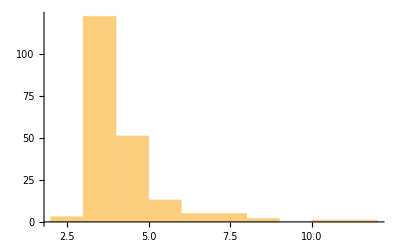

```mathematica
Histogram[CNs]
```